# G_4 classification

Let us start by loading the xIdeal package of xAct, which can be downloaded at https://github.com/wtbgagoa/xIdeal

```mathematica
<<xAct`xIdeal`
$DefInfoQ=False;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2026, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xIdeal`  version 0.1.0, {2025,10,29}

Copyright (C) 2023, Alfonso Garcia-Parrado Gomez-Lobo and Salvador Mengual Sendra, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Then, we define the manifold and chart

```mathematica
DefManifold[M,4,IndexRange[a,n]];
DefChart[chart,M,{0,1,2,3},{t[],x[],y[],z[]}];
```

and some constants that we will need:

```mathematica
DefConstantSymbol[s];
DefConstantSymbol[𝒶,PrintAs->"a"];
```

## Farnsworth-Kerr

```mathematica
ω1=dx-Sinh[y[]]dz;
ω2=Cos[x[]]dy-Sin[x[]]Cosh[y[]]dz;
ω3=Sin[x[]]dy+Cos[x[]]Cosh[y[]]dz;
```

#### Class II

```mathematica
UnsetCMetric[metric];
```

We start by defining the metric (40) and some constraints

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&1-4 s^2<0&&2-4 s^2>=0&&y[]∈Reals;
```

```mathematica
linelement=(1-s)ω3^2+(1+s)ω2^2-2 ω1^2+(dt+√(1-2 s^2)ω1)^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

First, let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
v=√2 𝒶 CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

In this case, we will obtain the connection tensor H by obtaining the Weyl principal frame:

```mathematica
w1=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
w2=CTensor[{Coefficient[ω2,dt],Coefficient[ω2,dx],Coefficient[ω2,dy],Coefficient[ω2,dz]},{-chart}];
w3=CTensor[{Coefficient[ω3,dt],Coefficient[ω3,dx],Coefficient[ω3,dy],Coefficient[ω3,dz]},{-chart}];
w4=CTensor[{1,0,0,0},{-chart}];
e0=𝒶 √2 w1;
e1=𝒶 w4+𝒶 √(1-2 s^2)w1;
e2=𝒶(√(1+s)w2+√(1-s)w3)/√2;
e3=𝒶(√(1+s)w2-√(1-s)w3)/√2;
```

With this, the connection tensor H can be obtained using the corresponding xIdeal function:

```mathematica
H=ConnectionTensor[metric,Rframe->{e0,e1,e2,e3},Verbose->False];
```

and the dimension of the isometry group is obtained by using its corresponding one:

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now, we perform the algorithm to classify the algebra:

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-a,-i],{-a}]//Simplify;𝒦[-a]===0
```

True

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

False

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

Then, this solution is of type U(3,+1).

#### Class III

For class III, the procedure is analogous:

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&s-1<0&&s+1>0;
```

```mathematica
linelement=(1-s)ω1^2+(1+s)ω2^2-2 ω3^2+dt^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√2 √(-metric[{0,-chart},{0,-chart}])),1/(√2 √(-metric[{1,-chart},{1,-chart}])),0,0},{chart}];v[a]v[-a]//Simplify
```

-1

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type D

In this case, we will obtain the connection tensor H by following the algorithm in Fig. 3. of [9]:

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}];
trS2=S2[a,-a];
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
P=Q/q;
Σ=HeadOfTensor[-1/2(CD[-a][P[-b,-m]]+CD[-b][P[-a,-m]])P[m,-l],{-a,-b,-l}]//Simplify;
𝓍=HeadOfTensor[-Σ[-b,-l,-m]Σ[-c,l,m]Σ[b,c,a],{a}]//Simplify;
σ2=HeadOfTensor[-Σ[-a,-l,-m]Σ[-b,l,m],{-a,-b}]//Simplify;
ασ=σ2[a,-a]//Simplify;
δσ=ασ^3-6𝓍[a]𝓍[-a]//Simplify;
KK=1/δσ(3ασ  σ2+6Σ[-a,-b,-c]𝓍[c]+1/2 ασ^2(metric+P))//Simplify;
J=HeadOfTensor[CD[-a][Σ[b,-c,-d]]Σ[c,e,-f]P[d,f]epsilon[metric][-b,-e,-g,-h]KK[g,i]epsilon[metric][-i,-j,-k,-l]P[h,l],{-a,-j,-k}]//Simplify;
ℐ=HeadOfTensor[-CD[-a][P[i,-b]]P[-c,-i]+CD[-a][P[i,-c]]P[-b,-i],{-a,-b,-c}]//Simplify;
H=ℐ-J//Simplify;
```

and the dimension of the isometry group is obtained by using the corresponding xIdeal function:

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]===0
```

True

Thus, the algebra is unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

False

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

Then, this solution is of type U(3,+1).

## Osvath-Koutras

```mathematica
A=1/2(1-β);
B=1/2(1+β);
F=1-s^2;
𝒷=√2 s(3-s^2);
β=√(1+2 s^2(1-s^2)(3-s^2));
```

### Class I (β^2>0)

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=s∈Reals&&𝒶∈Reals&&1-2 s^2<=0&&2-s^2>=0&&β^2>0;
```

```mathematica
metricMatrix=𝒶^2{{(4/𝒷^2 A^2-1)Exp[2A z[]],(4/𝒷^2 A B-1) Exp[(A+B)z[]],0,0},{(4/𝒷^2 A B-1) Exp[(A+B)z[]],(4/𝒷^2 B^2-1)Exp[2B z[]],0,0},{0,0,Exp[2F z[]],0},{0,0,0,1}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0
0
0
-2+s^2 |  
a

In this case, the algebra is non-unimodular.

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

Petrov Type VI.

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;𝒞tilde[c,-a,-b]===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;𝒞tilde2[a,-b,-c,-d]===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;𝒞tilde3[a,-b,-c,-d,-e]===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
ξ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6ξ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[Δtilde]
```

True

```mathematica
Δtilde
```

(s^4 (5-6 s^2+s^4)^2 (1+6 s^2-8 s^4+2 s^6))/(2 a^6)

```mathematica
Solve[1+6xx-8 xx^2+2 xx^3==0,xx];
ssv=N[%[[2]][[1]][[2]]]
```

1.22968

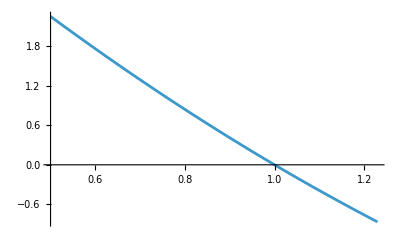

```mathematica
Plot[5-6 xx+xx^2,{xx,0.5,ssv}]
```

If Δ̃≠0 (s^2≠1):

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
Dtilde=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;Dtilde[-a,-b,-c]
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
-3 s^2 (-3+s^2) (-1+s^2)^2 |   |   |  
a | b | c

If Δ̃=0 (s^2=1):

```mathematica
Ptilde=HeadOfTensor[𝒞tilde2[a,-b,-c,-d]ℐtilde[-e,-f]-𝒞tilde[a,-b,-c]Jtilde[-d,-e,-f]-1/3 Antisymmetrize[metric[a,-b]ℐtilde[-c,-d]ℐtilde[-e,-f],{-b,-c}],{a,-b,-c,-d,-e,-f}]/.{s->-1}//Simplify;
Ptilde[a,-b,-c,-d,-e,-f]===0
```

False

```mathematica
Dtilde[-a,-b,-c]/.{s->-1}//Simplify
```

0

```mathematica
Qtilde=HeadOfTensor[ℐ[-a,-b]-𝒦[-a]𝒦[-b],{-a,-b}]/.{s->-1};
Qtilde===Zero
```

True

```mathematica
𝓍=CTensor[{0,0,0,1},{chart}];
κ𝓍=𝒦[-a]𝓍[a];
ν𝓍=ℐ[-a,-b]𝓍[a]𝓍[b]//Simplify;
ξ𝓍=J[-a,-b,-c]𝓍[a]𝓍[b]𝓍[c]//Simplify;
α=ν𝓍/κ𝓍^2//Simplify
β=ξ𝓍/κ𝓍^3//Simplify
```

(-1-s^2+s^4)/(-2+s^2)

-(4+3 s^2-6 s^4+s^6)/(2 (-2+s^2)^3)

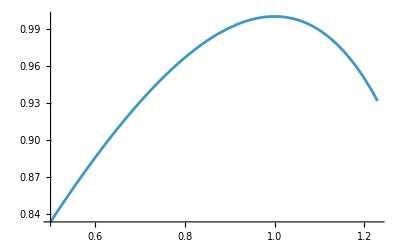

```mathematica
Plot[(-1-xx+xx^2)/(-2+xx),{xx,0.5,ssv}]
```

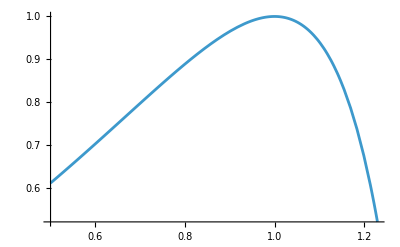

```mathematica
Plot[-(4+3 xx-6 xx^2+xx^3)/(2 (-2+xx)^3),{xx,0.5,ssv}]
```

```mathematica
{(-1-xx+xx^2)/(-2+xx)/.{xx->1},-(4+3 xx-6 xx^2+xx^3)/(2 (-2+xx)^3)/.{xx->1}}
```

{1,1}

```mathematica
{(-1-xx+xx^2)/(-2+xx)/.{xx->ssv},-(4+3 xx-6 xx^2+xx^3)/(2 (-2+xx)^3)/.{xx->ssv}}
```

{0.931517,0.520419}

### Class II (β^2=0)

```mathematica
UnsetCMetric[metric];
```

No definim les variables anteriors.

```mathematica
Clear[{A,B,F,𝒷,β}]
```

```mathematica
$Assumptions=𝒶∈Reals&&s∈Reals&&1+6 s^2-8 s^4+2 s^6==0;
```

```mathematica
betazero={s^6->(-1-6 s^2+8 s^4)/2};
```

```mathematica
Solve[a1 xx^3+a2 xx^2+a3 xx+a4==0,xx]/.{a1->2,a2->-8,a3->6,a4->1}//Simplify;
sv=√(%[[3]][[1]][[2]]);
metricMatrix=𝒶^2{{-1/4(𝒷-1/𝒷)^2 Exp[ z[]],-z[]/4(𝒷-1/𝒷)^2 Exp[ z[]],0,0},{-z[]/4(𝒷-1/𝒷)^2 Exp[ z[]],(1-z[]^2/4(𝒷-1/𝒷)^2)Exp[ z[]],0,0},{0,0,Exp[2F z[]],0},{0,0,0,1}}/.betazero//Simplify;
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
Solve[2 xx^3-8 xx^2+6 xx+1==0,xx];
svn=N[√(%[[2]][[1]][[2]])];
```

```mathematica
svn
```

1.10891

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

```mathematica
𝒲=xAct`xIdeal`Private`weylConcomitant["WeylSelfDual"][metric,Verbose->False];
𝒲2=HeadOfTensor[1/2 𝒲[-a,-b,-i,-j]𝒲[i,j,-c,-d],{-a,-b,-c,-d}];
𝒲3=HeadOfTensor[1/2 𝒲2[-a,-b,-i,-j]𝒲[i,j,-c,-d],{-a,-b,-c,-d}]//Simplify;
aa=1/2 𝒲2[-a,-b,a,b]//Simplify;
bb=1/2 𝒲3[-a,-b,a,b]//Simplify;
CD=CovDOfMetric[metric];
𝒳=HeadOfTensor[CD[-a][𝒲[-b,-c,-d,-e]] 𝒲[d,e,c,-f]/2,{-a,-b,-f}];
𝒢2=xAct`xIdeal`Private`metricConcomitant["G2Form"][metric,Verbose->False]//Simplify;
𝒴=(3 aa 𝒲2+6 bb 𝒲+aa^2 𝒢2/2)/(aa^3-6 bb^2)//Simplify;
ℋ=HeadOfTensor[𝒳[-a,-b,-c] 𝒴[b,c,-d,-e]/√2,{-a,-d,-e}]//Simplify;
```

```mathematica
A=1/2(1-β);
B=1/2(1+β);
F=1-s^2;
𝒷=√2 s(3-s^2);
β=√(1+2 s^2(1-s^2)(3-s^2));
```

```mathematica
H=(ℋ+Dagger[ℋ])/Sqrt[2]//Simplify;H[-a,-b,-c]
```

0
0
0
● | 0
0
0
● | 0
0
0
0 | ●
●
0
0
0
0
0
● | 0
0
0
● | 0
0
0
0 | ●
●
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
ⅇ^(-2 (-1+s^2) z) (-1+s^2) a^2 | 0
0
-ⅇ^(-2 (-1+s^2) z) (-1+s^2) a^2
0
0
●
0
0 | ●
0
0
0 | 0
0
0
0 | 0
0
0
0 |   |   |  
a | b | c

El que he fet es no definir ni 𝒷 ni F en funció d’s fins el càlcul d’H (no se si haguera funcionat fent-ho).

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]/.{s->svn}//Simplify
```

0
0
0
-0.770319 |  
a

```mathematica
s^2-2/.{s->svn}//Simplify
```

-0.770319

Thus, the algebra is non-unimodular.

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;(𝒞tilde[c,-a,-b]/.{s->svn}//Simplify)===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;(𝒞tilde2[a,-b,-c,-d]/.{s->svn}//Simplify)===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;(𝒞tilde3[a,-b,-c,-d,-e]/.{s->svn}//Simplify)===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
λ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6λ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[(Δtilde/.{s->svn}//Simplify)]
```

False

```mathematica
Δtilde/.{s->svn}//Simplify
```

0

```mathematica
Ptilde=HeadOfTensor[𝒞tilde2[a,-b,-c,-d]ℐtilde[-e,-f]-𝒞tilde[a,-b,-c]Jtilde[-d,-e,-f]-1/3 Antisymmetrize[metric[a,-b]ℐtilde[-c,-d]ℐtilde[-e,-f],{-b,-c}],{a,-b,-c,-d,-e,-f}]/.{s->-svn}//Simplify;
Ptilde[a,-b,-c,-d,-e,-f]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
S=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;(S[-a,-b,-c]/.{s->svn}//Simplify)===0
```

False

Therefore, this solution is of type N[21]. Let us obtain its parameters:

```mathematica
𝒦[a]𝒦[-a]/.{s->svn}//Simplify
```

0.593391/a^2

```mathematica
α=(ℐ[-a,-c]𝒦[a]𝒦[c])/(𝒦[-b]𝒦[b])^2/.{s->svn}//Simplify
```

0.931517

```mathematica
β=(J[-a,-b,-c]𝒦[a]𝒦[b]𝒦[c])/(𝒦[-d]𝒦[d])^3/.{s->svn}//Simplify
```

0.520419

```mathematica
2β-3α+1
```

-0.753713

```mathematica
{(ℐ[-a,-c]𝒦[a]𝒦[c])/(𝒦[-b]𝒦[b])^2/.{s->svn}//Simplify,(J[-a,-b,-c]𝒦[a]𝒦[b]𝒦[c])/(𝒦[-d]𝒦[d])^3/.{s->svn}//Simplify}
```

{0.931517,0.520419}

## Petrov solution

```mathematica
UnsetCMetric[metric];
```

```mathematica
DefConstantSymbol[kk,PrintAs->"k"];
$Assumptions=kk∈ Reals;
metricMatrix={{-E^x[] Cos[√3 x[]],0,0,-E^x[] Sin[√3 x[]]},{0,1,0,0},{0,0,E^(-2x[]),0},{-E^x[] Sin[√3 x[]],0,0,E^x[] Cos[√3 x[]]}}/kk^2;
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{E^(x[]/2)/(kk √Cos[√3 x[]]),0,0,0},{-chart}];v[a]v[-a]//Simplify
```

-1

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}];𝒦[-a]
```

0

Unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}];L[e,-a,-b,-c,-d]
```

0

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];𝒞2[d,-a,-b,-c]===0
```

False

```mathematica
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;𝒞3[e,-a,-b,-c,-d]===0
```

False

```mathematica
ℐ=HeadOfTensor[𝒞2[a,-a,-b,-c],{-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
λ2=γ[e,f]γ[a,c]γ[b,d]J[-a,-c,-e]J[-b,-d,-f];
Δ=ν^3-6λ2//Simplify
```

-54 k^6

```mathematica
J[-a,-b,-c]===0
```

False

## 12.21

```mathematica
UnsetCMetric[metric];
```

```mathematica
$Assumptions=𝒶∈Reals;
```

```mathematica
metricMatrix={{-1,0,0,2y[]},{0,𝒶^2/x[]^2,0,0},{0,0,𝒶^2/x[]^2,0},{2y[],0,0,x[]^2-4 y[]^2}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{1/(√(-metric[{0,-chart},{0,-chart}])),0,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type I

```mathematica
H=ConnectionTensor[metric,Verbose->False];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0

Unimodular.

```mathematica
L=HeadOfTensor[𝒞[i,-a,-b]𝒞[j,-c,-d]𝒞[e,-i,-j],{e,-a,-b,-c,-d}]//Simplify;L[e,-a,-b,-c,-d]===0
```

False

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}];
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
ℐ=HeadOfTensor[𝒞2[a,-a,-b,-c],{-b,-c}];
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}];
J[-a,-b,-c]===0
```

True

```mathematica
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
ν=γ[a,b]ℐ[-a,-b]//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[ν]
```

True

## 12.35

```mathematica
UnsetCMetric[metric];
```

```mathematica
DefConstantSymbol[Λ];
```

```mathematica
$Assumptions=Λ∈Reals&&Λ>0&&z[]∈Reals;
```

```mathematica
metricMatrix={{0,E^(-2z[]),0,0},{E^(-2z[]),E^(4z[]),2 E^z[],0},{0,2 E^z[],2 E^(-2z[]),0},{0,0,0,3/Λ}};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

```mathematica
v=CTensor[{(1+E^(4z[]))/2 E^(2z[]),-1,0,0},{chart}];v[a]v[-a]//Simplify
```

-1

Let us determine its Petrov Type by using the corresponding xIdeal function:

```mathematica
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->v]
```

Type III

```mathematica
X=CTensor[{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{1,0,0,0}},{-chart,-chart}];𝒲2=xAct`xIdeal`Private`weylConcomitant["WeylSelfDual2"][metric,Verbose->False];𝒲2[-a,-b,-c,-d]X[c,d]
```

0 | 0 | 0 | 0
0 | 0 | (ⅈ ⅇ^(5 z) Λ^(5/2))/(√6) | -1/2 ⅇ^(6 z) Λ^2
0 | -(ⅈ ⅇ^(5 z) Λ^(5/2))/(√6) | 0 | 0
0 | 1/2 ⅇ^(6 z) Λ^2 | 0 | 0 |   |  
a | b

```mathematica
H=ConnectionTensor[metric,Verbose->False,"Bivector"->X];
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

```mathematica
𝒞=HeadOfTensor[-2Antisymmetrize[H[-a,-b,c],{-a,-b}],{c,-a,-b}];
𝒦=HeadOfTensor[𝒞[i,-i,-a],{-a}]//Simplify;𝒦[-a]
```

0
0
0
3 |  
a

```mathematica
nn=HeadOfTensor[1/2 epsilon[metric][a,c,d,e]𝒦[-c]𝒞[b,-d,-e],{a,b}]//Simplify
```

Zero

```mathematica
𝒞tilde=HeadOfTensor[𝒞[c,-a,-b]-1/3 2Antisymmetrize[metric[c,-a]𝒦[-b],{-a,-b}],{c,-a,-b}]//Simplify;𝒞tilde[c,-a,-b]===0
```

False

```mathematica
𝒞tilde2=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde[c,-i,-d],{c,-a,-b,-d}]//Simplify;𝒞tilde2[a,-b,-c,-d]===0
```

False

```mathematica
𝒞tilde3=HeadOfTensor[𝒞tilde[i,-a,-b]𝒞tilde2[c,-i,-d,-e],{c,-a,-b,-d,-e}]//Simplify;𝒞tilde3[a,-b,-c,-d,-e]===0
```

False

```mathematica
ℐtilde=HeadOfTensor[𝒞tilde2[-a,a,-b,-c],{-b,-c}];
Jtilde=HeadOfTensor[𝒞tilde3[i,-i,-a,-b,-c],{-a,-b,-c}];
γ=HeadOfTensor[metric[-a,-b]+2v[-a]v[-b],{-a,-b}];
νtilde=γ[a,b]ℐtilde[-a,-b]//Simplify;
μtilde=γ[a,c]γ[b,d]ℐtilde[-a,-b]ℐtilde[-c,-d]//Simplify;
σtilde=νtilde^2-μtilde//Simplify;
λ2tilde=γ[e,f]γ[a,c]γ[b,d]Jtilde[-a,-c,-e]Jtilde[-b,-d,-f]//Simplify;
Δtilde=νtilde^3-6λ2tilde//Simplify;
xAct`xIdeal`Private`SymbolicPositiveQ[Δtilde]
```

True

```mathematica
𝒞2=HeadOfTensor[𝒞[i,-b,-c]𝒞[a,-i,-d],{a,-b,-c,-d}]//Simplify;
ℐ=HeadOfTensor[𝒞2[-a,a,-b,-c],{-b,-c}]//Simplify;
𝒞3=HeadOfTensor[𝒞[i,-b,-c]𝒞2[a,-i,-d,-e],{a,-b,-c,-d,-e}]//Simplify;
J=HeadOfTensor[𝒞3[i,-i,-a,-b,-c],{-a,-b,-c}]//Simplify;
S=HeadOfTensor[2J[-a,-b,-c]-3ℐ[-a,-b]𝒦[-c]+𝒦[-a]𝒦[-b]𝒦[-c],{-a,-b,-c}]//Simplify;S[-a,-b,-c]
```

0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
-48 |   |   |  
a | b | c

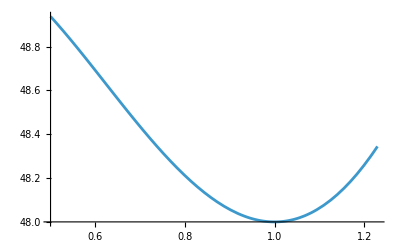

```mathematica
Plot[-3 xx(-3+xx) (-1+xx)^2+48,{xx,0.5,ssv}]
```

```mathematica
xx=CTensor[{0,0,0,1},{chart}];
κx=𝒦[-a]xx[a]
```

3

```mathematica
νx=ℐ[-a,-b]xx[a]xx[b]//Simplify
```

21

```mathematica
ξx=J[-a,-b,-c]xx[a]xx[b]xx[c]//Simplify
```

57

```mathematica
α=νx/κx^2//Simplify
```

7/3

```mathematica
β=ξx/κx^3//Simplify
```

19/9

```mathematica
N[β]
```

2.11111